```mathematica
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\Direct_Greens_Function\\bin"];
```

```mathematica
gData=Flatten[Import["greens.dat","Table"]];
```

```mathematica
t=1.0;
J=0.4t;
Emin=-6;
Emax=8;
```

```mathematica
GF=Table[
(w=(Emax-Emin)*(it-1)/(Length[gData]-1)+Emin;
z=ToExpression[StringJoin["{",StringTake[gData[[it]],{2;;-2}],"}"]];
{w,z[[1]]+I z[[2]]}
),
{it, 1,Length[gData]}];
```

```mathematica
rotGF[GF_,m4_]:=(
d=0.05;
w0=2J;
w=Table[GF[[it,1]],{it,1,Length[GF]}]+I d;
G0=1/(w-w0);
invG0=G0^-1;
invG=GF[[;;,2]]^-1;
EGE=(4t^2)^-1/((invG0-invG)^-1 -(invG0+3invG)^-1);
PGP=(4t^2)^-1/((invG0-invG)^-1 - G0);
NGE=(PGP-EGE)/3;
res=EGE+(Exp[I Pi m4/2]+Exp[I Pi m4]+Exp[3I Pi m4/2])NGE;
Table[{GF[[it,1]],res[[it]]},{it,1,Length[GF]}]
)
```

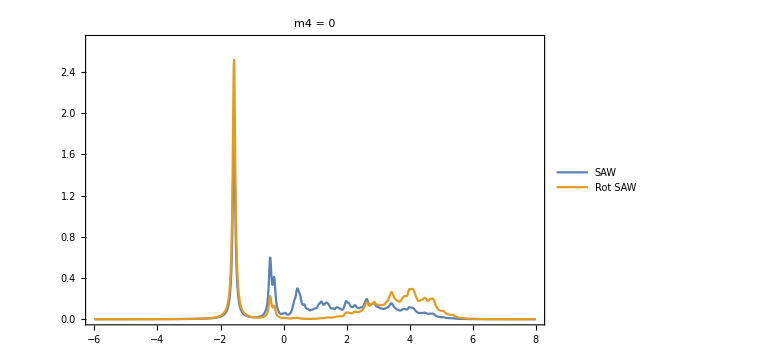

```mathematica
rGF=rotGF[GF,0];
fig=ListLinePlot[{Table[{GF[[it,1]],-Im[GF[[it,2]]]/Pi},{it,1,Length[GF]}],Table[{rGF[[it,1]],-Im[rGF[[it,2]]]/Pi},{it,1,Length[rGF]}]},
PlotRange->{{Emin,Emax},{0,2.7}},Frame->True,Axes->{True,False},ImageSize->Large,
PlotLegends->Placed[{Style["SAW",20,Black,FontFamily->"Book Oldman Style"],Style["Rot SAW",20,Black,FontFamily->"Book Oldman Style"]},{0.8,0.8}],
FrameStyle->Directive[Black, 16],
PlotLabel->Style["m4 = 0",20,Black,FontFamily->"Book Oldman Style"]
]
```

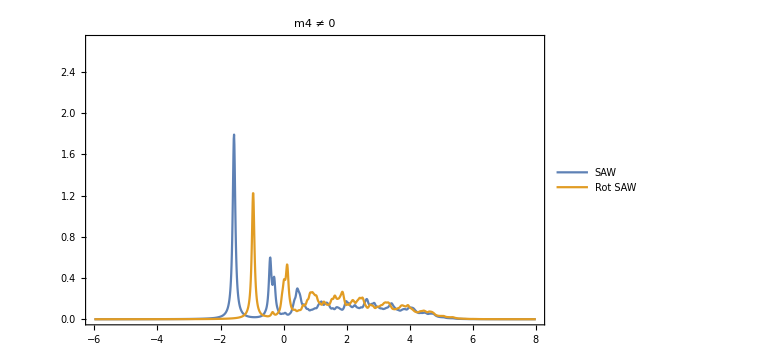

```mathematica
rGF=rotGF[GF,1];
fig=ListLinePlot[{Table[{GF[[it,1]],-Im[GF[[it,2]]]/Pi},{it,1,Length[GF]}],Table[{rGF[[it,1]],-Im[rGF[[it,2]]]/Pi},{it,1,Length[rGF]}]},
PlotRange->{{Emin,Emax},{0,2.7}},Frame->True,Axes->{True,False},ImageSize->Large,
PlotLegends->Placed[{Style["SAW",20,Black,FontFamily->"Book Oldman Style"],Style["Rot SAW",20,Black,FontFamily->"Book Oldman Style"]},{0.8,0.8}],
FrameStyle->Directive[Black, 16],
PlotLabel->Style["m4 ≠ 0",20,Black,FontFamily->"Book Oldman Style"]
]
```

```mathematica
gData=Flatten[Import["greens_hm.dat","Table"]];
```

```mathematica
GF=Table[
(w=(Emax-Emin)*(it-1)/(Length[gData]-1)+Emin;
z=ToExpression[StringJoin["{",StringTake[gData[[it]],{2;;-2}],"}"]];
{w,z[[1]]+I z[[2]]}
),
{it, 1,Length[gData]}];
```

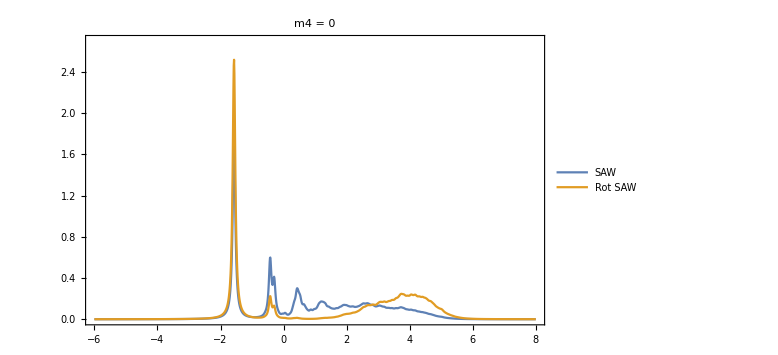

```mathematica
rGF=rotGF[GF,0];
fig=ListLinePlot[{Table[{GF[[it,1]],-Im[GF[[it,2]]]/Pi},{it,1,Length[GF]}],Table[{rGF[[it,1]],-Im[rGF[[it,2]]]/Pi},{it,1,Length[rGF]}]},
PlotRange->{{Emin,Emax},{0,2.7}},Frame->True,Axes->{True,False},ImageSize->Large,
PlotLegends->Placed[{Style["SAW",20,Black,FontFamily->"Book Oldman Style"],Style["Rot SAW",20,Black,FontFamily->"Book Oldman Style"]},{0.8,0.8}],
FrameStyle->Directive[Black, 16],
PlotLabel->Style["m4 = 0",20,Black,FontFamily->"Book Oldman Style"]
]
```

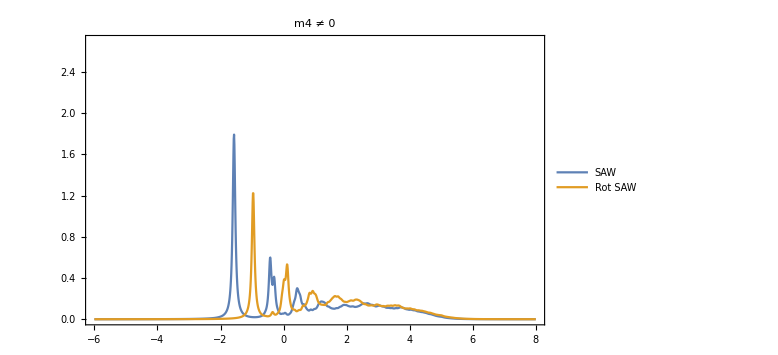

```mathematica
rGF=rotGF[GF,1];
fig=ListLinePlot[{Table[{GF[[it,1]],-Im[GF[[it,2]]]/Pi},{it,1,Length[GF]}],Table[{rGF[[it,1]],-Im[rGF[[it,2]]]/Pi},{it,1,Length[rGF]}]},
PlotRange->{{Emin,Emax},{0,2.7}},Frame->True,Axes->{True,False},ImageSize->Large,
PlotLegends->Placed[{Style["SAW",20,Black,FontFamily->"Book Oldman Style"],Style["Rot SAW",20,Black,FontFamily->"Book Oldman Style"]},{0.8,0.8}],
FrameStyle->Directive[Black, 16],
PlotLabel->Style["m4 ≠ 0",20,Black,FontFamily->"Book Oldman Style"]
]
```

```mathematica
Total[-Im[rGF][[;;,2]]]/Pi*0.01
Total[-Im[GF][[;;,2]]]/Pi*0.01
```

0.995106

0.995016

```mathematica
testGF[GF_]:=(
d=0.05;
w0=2J;
w=Table[GF[[it,1]],{it,1,Length[GF]}]+I d;
G0=1/(w-w0);
invG0=G0^-1;
invG=GF[[;;,2]]^-1;
res=1/((4t^2)/(invG0-invG)-(4t^2)/(invG0));
Table[{GF[[it,1]],res[[it]]},{it,1,Length[GF]}]
)
```

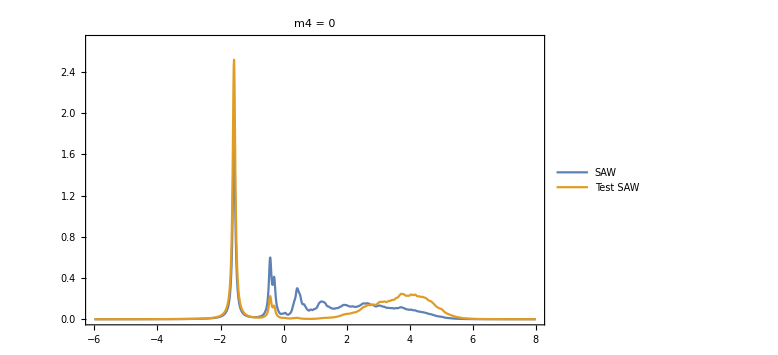

```mathematica
tGF=testGF[GF];
fig=ListLinePlot[{Table[{GF[[it,1]],-Im[GF[[it,2]]]/Pi},{it,1,Length[GF]}],Table[{tGF[[it,1]],-Im[tGF[[it,2]]]/Pi},{it,1,Length[tGF]}]},
PlotRange->{{Emin,Emax},{0,2.7}},Frame->True,Axes->{True,False},ImageSize->Large,
PlotLegends->Placed[{Style["SAW",20,Black,FontFamily->"Book Oldman Style"],Style["Test SAW",20,Black,FontFamily->"Book Oldman Style"]},{0.8,0.8}],
FrameStyle->Directive[Black, 16],
PlotLabel->Style["m4 = 0",20,Black,FontFamily->"Book Oldman Style"]
]
```

```mathematica
genWF[m4_]:=(
dir=<|0->"E",1->"N",2->"W",3->"S"|>;
phase[rm4_]:=Exp[I Pi rm4 /2];
resWF={{1,""}};
For[it=1,it≤Length[m4],it++,(
oldWF=resWF;
resWF={};
For[s=1,s≤Length[oldWF],s++,(
For[r=0,r<4,r++,(
newTerm={oldWF[[s,1]]*phase[r m4[[it]]],StringJoin[oldWF[[s,2]],dir[r]]};
AppendTo[resWF,newTerm];
)];
)];
)];
resWF)
```

```mathematica
Table[{m1,m2,genWF[{m1,m2}]},{m1,0,3},{m2,0,3}]//TableForm;
```